## Introduction

Want to study the stability of the static two cluster state. Fixed points are

(x_1,θ_1) and (x_2,θ_2)=(x_1+C(parameters), θ_1+π/2)

```mathematica
Solve[x'[t]+x[t]==10,x]
```

## Main

### Jacobian

```mathematica
(*Jacobian*)
{j,n}={1,3};
xdot=Table[j/n Sum[Sin[Subscript[x, j]-Subscript[x, i]]Cos[Subscript[θ, j]-Subscript[θ, i]],{j,1,n}],{i,1,n}];
thetadot=Table[Δ-F Sin[Subscript[θ, i]]-k/n Sum[Sin[Subscript[θ, j]-Subscript[θ, i]]Cos[Subscript[x, j]-Subscript[x, i]],{j,1,n}],{i,1,n}];
eqnsdot=Join[{xdot,thetadot}]//Flatten;
J=Table[Join[Table[D[eqnsdot[[l]], Subscript[x, i]],{i,1,n}],Table[D[eqnsdot[[l]], Subscript[θ, i]],{i,1,n}]],{l,1,Length[eqnsdot]}];

(*Fixed points*)
subs1=Join[{Table[Subscript[θ, i]->π/4,{i,1,Floor[n/2]}],Table[Subscript[θ, i]->-π/4,{i,Floor[n/2]+1,n}]}];
subs2=Join[{Table[Subscript[x, i]->c,{i,1,Floor[n/2]}],Table[Subscript[x, i]->c+ArcCos[√2 F/k],{i,Floor[n/2]+1,n}]}];
subs=Flatten[Join[subs1,subs2]];

TableForm[J/.subs]
```

0 | 0 | 0 | -2/3 √(1-(2 F^2)/k^2) | 1/3 √(1-(2 F^2)/k^2) | 1/3 √(1-(2 F^2)/k^2)
0 | -1/3 | 1/3 | 1/3 √(1-(2 F^2)/k^2) | -1/3 √(1-(2 F^2)/k^2) | 0
0 | 1/3 | -1/3 | 1/3 √(1-(2 F^2)/k^2) | 0 | -1/3 √(1-(2 F^2)/k^2)
2/3 √(1-(2 F^2)/k^2) k | -1/3 √(1-(2 F^2)/k^2) k | -1/3 √(1-(2 F^2)/k^2) k | -F/(√2) | 0 | 0
-1/3 √(1-(2 F^2)/k^2) k | 1/3 √(1-(2 F^2)/k^2) k | 0 | 0 | -F/(√2)+k/3 | -k/3
-1/3 √(1-(2 F^2)/k^2) k | 0 | 1/3 √(1-(2 F^2)/k^2) k | 0 | -k/3 | -F/(√2)+k/3

### Eigenvalues

#### n = 3

```mathematica
(*Jacobian*)
{j,n}={1,3};
xdot=Table[j/n Sum[Sin[Subscript[x, j]-Subscript[x, i]]Cos[Subscript[θ, j]-Subscript[θ, i]],{j,1,n}],{i,1,n}];
thetadot=Table[Δ-F Sin[Subscript[θ, i]]-k/n Sum[Sin[Subscript[θ, j]-Subscript[θ, i]]Cos[Subscript[x, j]-Subscript[x, i]],{j,1,n}],{i,1,n}];
eqnsdot=Join[{xdot,thetadot}]//Flatten;
J=Table[Join[Table[D[eqnsdot[[l]], Subscript[x, i]],{i,1,n}],Table[D[eqnsdot[[l]], Subscript[θ, i]],{i,1,n}]],{l,1,Length[eqnsdot]}];

(*Fixed points*)
subs1=Join[{Table[Subscript[θ, i]->π/4,{i,1,Floor[n/2]}],Table[Subscript[θ, i]->π/4+π/2,{i,Floor[n/2]+1,n}]}];
subs2=Join[{Table[Subscript[x, i]->c,{i,1,Floor[n/2]}],Table[Subscript[x, i]->c+ArcCos[√2 F/k],{i,Floor[n/2]+1,n}]}];
subs=Flatten[Join[subs1,subs2]];

λ=Eigenvalues[J/.subs];
TableForm[λ]
```

0
-(4 k-3 √2 F k-4 k^2+√((-4 k+3 √2 F k+4 k^2)^2+4 k (8 F^2+12 √2 F k+12 k^2)))/(12 k)
(-4 k+3 √2 F k+4 k^2+√((-4 k+3 √2 F k+4 k^2)^2+4 k (8 F^2+12 √2 F k+12 k^2)))/(12 k)
1/6 Root[144 F^3-72 F k^2+(-72 √2 F^2-18 √2 F^2 k+36 √2 k^2) #1+√2 k #1^3&,1]
1/6 Root[144 F^3-72 F k^2+(-72 √2 F^2-18 √2 F^2 k+36 √2 k^2) #1+√2 k #1^3&,2]
1/6 Root[144 F^3-72 F k^2+(-72 √2 F^2-18 √2 F^2 k+36 √2 k^2) #1+√2 k #1^3&,3]

So I need these all to have Re(λ) < 0... That means F > 0 only?

```mathematica
Solve[-(4 k-3 √2 F k-4 k^2+√((-4 k+3 √2 F k+4 k^2)^2+4 k (8 F^2+12 √2 F k+12 k^2)))/(12 k)==0,F]//FullSimplify
```

{{F→k Root-1.06-0.612 ⅈRoot[9-6 #1^2+4 #1^4&,1]-1.0606601717798212},{F→k Root-1.06+0.612 ⅈRoot[9-6 #1^2+4 #1^4&,2]-1.0606601717798212}}

```mathematica
J
```

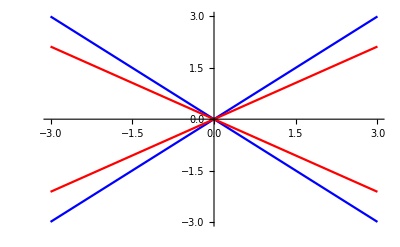

```mathematica
Plot[{k,-k,k/(√2),-k/(√2)},{k,-3,3},PlotStyle->{Blue,Blue,Red,Red}]
```

```mathematica
Clear[λ]
```

```mathematica
IdentityMatrix[3]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
J/.subs
```

{{0,0,0,2/3 √(1-(2 F^2)/k^2),-1/3 √(1-(2 F^2)/k^2),-1/3 √(1-(2 F^2)/k^2)},{0,-1/3,1/3,-1/3 √(1-(2 F^2)/k^2),1/3 √(1-(2 F^2)/k^2),0},{0,1/3,-1/3,-1/3 √(1-(2 F^2)/k^2),0,1/3 √(1-(2 F^2)/k^2)},{-2/3 √(1-(2 F^2)/k^2) k,1/3 √(1-(2 F^2)/k^2) k,1/3 √(1-(2 F^2)/k^2) k,-F/(√2),0,0},{1/3 √(1-(2 F^2)/k^2) k,-1/3 √(1-(2 F^2)/k^2) k,0,0,F/(√2)+k/3,-k/3},{1/3 √(1-(2 F^2)/k^2) k,0,-1/3 √(1-(2 F^2)/k^2) k,0,-k/3,F/(√2)+k/3}}

```mathematica
eqn=Collect[Det[(J/.subs)-λ IdentityMatrix[2n]],λ,Simplify]
```

-(F (2 F^2-k^2) (2 √2 F^2+6 F k+3 √2 k^2) λ)/(54 k^2)-((4 F^4 (-2+k)+√2 F^3 (-16+k) k-2 √2 F (-4+k) k^3+6 k^4-2 F^2 k^2 (4+3 k)) λ^2)/(18 k^2)+((-8 √2 F k^2-8 (-1+k) k^2+√2 F^3 (16+3 k)+4 F^2 (-4+3 k+k^2)) λ^3)/(12 k)+1/18 (-6 √2 F+F^2 (-9-40/k)+12 k) λ^4+1/6 (4-3 √2 F-4 k) λ^5+λ^6

```mathematica
eqn/.λ->ⅈ ω
```

-(ⅈ F (2 F^2-k^2) (2 √2 F^2+6 F k+3 √2 k^2) ω)/(54 k^2)+((4 F^4 (-2+k)+√2 F^3 (-16+k) k-2 √2 F (-4+k) k^3+6 k^4-2 F^2 k^2 (4+3 k)) ω^2)/(18 k^2)-(ⅈ (-8 √2 F k^2-8 (-1+k) k^2+√2 F^3 (16+3 k)+4 F^2 (-4+3 k+k^2)) ω^3)/(12 k)+1/18 (-6 √2 F+F^2 (-9-40/k)+12 k) ω^4+1/6 ⅈ (4-3 √2 F-4 k) ω^5-ω^6

```mathematica
$Assumptions={{F,k,ω}∈Reals}
```

{(F|k|ω)∈ℝ}

```mathematica
e1=ComplexExpand[Re[eqn/.λ->ⅈ ω]];
e2=ComplexExpand[Im[eqn/.λ->ⅈ ω]]
```

-2/27 √2 F^3 ω-(2 √2 F^5 ω)/(27 k^2)-(2 F^4 ω)/(9 k)+1/9 F^2 k ω+(F k^2 ω)/(9 √2)-F^2 ω^3-(F^3 ω^3)/(2 √2)+(4 F^2 ω^3)/(3 k)-(4 √2 F^3 ω^3)/(3 k)-(2 k ω^3)/3+2/3 √2 F k ω^3-1/3 F^2 k ω^3+(2 k^2 ω^3)/3+(2 ω^5)/3-(F ω^5)/(√2)-(2 k ω^5)/3

```mathematica
Solve[{e1==0,e2==0},{F,k}]
```

$Aborted

#### n = 5

```mathematica
(*Jacobian*)
{j,n}={1,5};
xdot=Table[j/n Sum[Sin[Subscript[x, j]-Subscript[x, i]]Cos[Subscript[θ, j]-Subscript[θ, i]],{j,1,n}],{i,1,n}];
thetadot=Table[Δ-F Sin[Subscript[θ, i]]-k/n Sum[Sin[Subscript[θ, j]-Subscript[θ, i]]Cos[Subscript[x, j]-Subscript[x, i]],{j,1,n}],{i,1,n}];
eqnsdot=Join[{xdot,thetadot}]//Flatten;
J=Table[Join[Table[D[eqnsdot[[l]], Subscript[x, i]],{i,1,n}],Table[D[eqnsdot[[l]], Subscript[θ, i]],{i,1,n}]],{l,1,Length[eqnsdot]}];

(*Fixed points*)
subs1=Join[{Table[Subscript[θ, i]->π/4,{i,1,Floor[n/2]}],Table[Subscript[θ, i]->-π/4,{i,Floor[n/2]+1,n}]}];
subs2=Join[{Table[Subscript[x, i]->c,{i,1,Floor[n/2]}],Table[Subscript[x, i]->c+ArcCos[√2 F/k],{i,Floor[n/2]+1,n}]}];
subs=Flatten[Join[subs1,subs2]];

λ=Eigenvalues[J/.subs];
TableForm[λ]
```

0
1/10 Root[73728000 √2 F^9-317440000 F^8 k+241216000 √2 F^7 k^2-60480000 F^6 k^3-123840000 √2 F^5 k^4+141600000 F^4 k^5-15600000 √2 F^3 k^6-16000000 F^2 k^7+4000000 √2 F k^8+(14745600 F^8-63488000 √2 F^7 k-60006400 F^8 k+130803200 F^6 k^2+114880000 √2 F^7 k^2-26496000 √2 F^5 k^3-139104000 F^6 k^3-61248000 F^4 k^4-3672000 √2 F^5 k^4+35520000 √2 F^3 k^5+75120000 F^4 k^5-5520000 F^2 k^6-26160000 √2 F^3 k^6-3200000 √2 F k^7+800000 F^2 k^7+800000 k^8+1600000 √2 F k^8) #1+(-6348800 F^6 k-12001280 √2 F^7 k+12384000 √2 F^5 k^2+56230400 F^6 k^2+8208000 √2 F^7 k^2-8409600 F^4 k^3-38284800 √2 F^5 k^3-28387200 F^6 k^3-5472000 √2 F^3 k^4-1022400 F^4 k^4+13962000 √2 F^5 k^4+6432000 F^2 k^5+19104000 √2 F^3 k^5+3384000 F^4 k^5-360000 √2 F k^6-11472000 F^2 k^6-6504000 √2 F^3 k^6-320000 k^7+160000 √2 F k^7+3120000 F^2 k^7+320000 k^8-120000 √2 F k^8) #1^2+(-1200128 F^6 k+825600 F^4 k^2+4988160 √2 F^5 k^2+4924800 F^6 k^2-576000 √2 F^3 k^3-8014080 F^4 k^3-8029440 √2 F^5 k^3-840000 F^6 k^3-364800 F^2 k^4+100800 √2 F^3 k^4+7146000 F^4 k^4+1376000 √2 F^5 k^4+288000 √2 F k^5+3542400 F^2 k^5+1180800 √2 F^3 k^5-1266400 F^4 k^5-24000 k^6-936000 √2 F k^6-3172800 F^2 k^6-108000 √2 F^3 k^6+16000 k^7+624000 √2 F k^7+408000 F^2 k^7-24000 k^8-72000 √2 F k^8) #1^3+(332544 F^4 k^2+492480 √2 F^5 k^2-28800 F^2 k^3-418560 √2 F^3 k^3-1743744 F^4 k^3-336000 √2 F^5 k^3+54720 F^2 k^4+737040 √2 F^3 k^4+905600 F^4 k^4+12500 √2 F^5 k^4+14400 k^5+163200 √2 F k^5+319680 F^2 k^5-297280 √2 F^3 k^5-40000 F^4 k^5-62400 k^6-280800 √2 F k^6-122400 F^2 k^6+21000 √2 F^3 k^6+62400 k^7+81600 √2 F k^7-7200 F^2 k^7-14400 k^8) #1^4+(32832 F^4 k^2-20928 F^2 k^3-94080 √2 F^3 k^3-100800 F^4 k^3+3600 √2 F k^4+77136 F^2 k^4+110560 √2 F^3 k^4+12500 F^4 k^4+8160 k^5+20160 √2 F k^5-47328 F^2 k^5-16000 √2 F^3 k^5-18720 k^6-15120 √2 F k^6+12600 F^2 k^6+8160 k^7-1440 √2 F k^7) #1^5+(-4704 F^2 k^3-6720 √2 F^3 k^3+144 k^4+2100 √2 F k^4+12704 F^2 k^4+2500 √2 F^3 k^4+1008 k^5-1760 √2 F k^5-4800 F^2 k^5-1008 k^6+1260 √2 F k^6-144 k^7) #1^6+(-336 F^2 k^3+84 k^4+400 √2 F k^4+500 F^2 k^4-88 k^5-320 √2 F k^5+84 k^6) #1^7+(16 k^4+25 √2 F k^4-16 k^5) #1^8+k^4 #1^9&,1]
1/10 Root[73728000 √2 F^9-317440000 F^8 k+241216000 √2 F^7 k^2-60480000 F^6 k^3-123840000 √2 F^5 k^4+141600000 F^4 k^5-15600000 √2 F^3 k^6-16000000 F^2 k^7+4000000 √2 F k^8+(14745600 F^8-63488000 √2 F^7 k-60006400 F^8 k+130803200 F^6 k^2+114880000 √2 F^7 k^2-26496000 √2 F^5 k^3-139104000 F^6 k^3-61248000 F^4 k^4-3672000 √2 F^5 k^4+35520000 √2 F^3 k^5+75120000 F^4 k^5-5520000 F^2 k^6-26160000 √2 F^3 k^6-3200000 √2 F k^7+800000 F^2 k^7+800000 k^8+1600000 √2 F k^8) #1+(-6348800 F^6 k-12001280 √2 F^7 k+12384000 √2 F^5 k^2+56230400 F^6 k^2+8208000 √2 F^7 k^2-8409600 F^4 k^3-38284800 √2 F^5 k^3-28387200 F^6 k^3-5472000 √2 F^3 k^4-1022400 F^4 k^4+13962000 √2 F^5 k^4+6432000 F^2 k^5+19104000 √2 F^3 k^5+3384000 F^4 k^5-360000 √2 F k^6-11472000 F^2 k^6-6504000 √2 F^3 k^6-320000 k^7+160000 √2 F k^7+3120000 F^2 k^7+320000 k^8-120000 √2 F k^8) #1^2+(-1200128 F^6 k+825600 F^4 k^2+4988160 √2 F^5 k^2+4924800 F^6 k^2-576000 √2 F^3 k^3-8014080 F^4 k^3-8029440 √2 F^5 k^3-840000 F^6 k^3-364800 F^2 k^4+100800 √2 F^3 k^4+7146000 F^4 k^4+1376000 √2 F^5 k^4+288000 √2 F k^5+3542400 F^2 k^5+1180800 √2 F^3 k^5-1266400 F^4 k^5-24000 k^6-936000 √2 F k^6-3172800 F^2 k^6-108000 √2 F^3 k^6+16000 k^7+624000 √2 F k^7+408000 F^2 k^7-24000 k^8-72000 √2 F k^8) #1^3+(332544 F^4 k^2+492480 √2 F^5 k^2-28800 F^2 k^3-418560 √2 F^3 k^3-1743744 F^4 k^3-336000 √2 F^5 k^3+54720 F^2 k^4+737040 √2 F^3 k^4+905600 F^4 k^4+12500 √2 F^5 k^4+14400 k^5+163200 √2 F k^5+319680 F^2 k^5-297280 √2 F^3 k^5-40000 F^4 k^5-62400 k^6-280800 √2 F k^6-122400 F^2 k^6+21000 √2 F^3 k^6+62400 k^7+81600 √2 F k^7-7200 F^2 k^7-14400 k^8) #1^4+(32832 F^4 k^2-20928 F^2 k^3-94080 √2 F^3 k^3-100800 F^4 k^3+3600 √2 F k^4+77136 F^2 k^4+110560 √2 F^3 k^4+12500 F^4 k^4+8160 k^5+20160 √2 F k^5-47328 F^2 k^5-16000 √2 F^3 k^5-18720 k^6-15120 √2 F k^6+12600 F^2 k^6+8160 k^7-1440 √2 F k^7) #1^5+(-4704 F^2 k^3-6720 √2 F^3 k^3+144 k^4+2100 √2 F k^4+12704 F^2 k^4+2500 √2 F^3 k^4+1008 k^5-1760 √2 F k^5-4800 F^2 k^5-1008 k^6+1260 √2 F k^6-144 k^7) #1^6+(-336 F^2 k^3+84 k^4+400 √2 F k^4+500 F^2 k^4-88 k^5-320 √2 F k^5+84 k^6) #1^7+(16 k^4+25 √2 F k^4-16 k^5) #1^8+k^4 #1^9&,2]
1/10 Root[73728000 √2 F^9-317440000 F^8 k+241216000 √2 F^7 k^2-60480000 F^6 k^3-123840000 √2 F^5 k^4+141600000 F^4 k^5-15600000 √2 F^3 k^6-16000000 F^2 k^7+4000000 √2 F k^8+(14745600 F^8-63488000 √2 F^7 k-60006400 F^8 k+130803200 F^6 k^2+114880000 √2 F^7 k^2-26496000 √2 F^5 k^3-139104000 F^6 k^3-61248000 F^4 k^4-3672000 √2 F^5 k^4+35520000 √2 F^3 k^5+75120000 F^4 k^5-5520000 F^2 k^6-26160000 √2 F^3 k^6-3200000 √2 F k^7+800000 F^2 k^7+800000 k^8+1600000 √2 F k^8) #1+(-6348800 F^6 k-12001280 √2 F^7 k+12384000 √2 F^5 k^2+56230400 F^6 k^2+8208000 √2 F^7 k^2-8409600 F^4 k^3-38284800 √2 F^5 k^3-28387200 F^6 k^3-5472000 √2 F^3 k^4-1022400 F^4 k^4+13962000 √2 F^5 k^4+6432000 F^2 k^5+19104000 √2 F^3 k^5+3384000 F^4 k^5-360000 √2 F k^6-11472000 F^2 k^6-6504000 √2 F^3 k^6-320000 k^7+160000 √2 F k^7+3120000 F^2 k^7+320000 k^8-120000 √2 F k^8) #1^2+(-1200128 F^6 k+825600 F^4 k^2+4988160 √2 F^5 k^2+4924800 F^6 k^2-576000 √2 F^3 k^3-8014080 F^4 k^3-8029440 √2 F^5 k^3-840000 F^6 k^3-364800 F^2 k^4+100800 √2 F^3 k^4+7146000 F^4 k^4+1376000 √2 F^5 k^4+288000 √2 F k^5+3542400 F^2 k^5+1180800 √2 F^3 k^5-1266400 F^4 k^5-24000 k^6-936000 √2 F k^6-3172800 F^2 k^6-108000 √2 F^3 k^6+16000 k^7+624000 √2 F k^7+408000 F^2 k^7-24000 k^8-72000 √2 F k^8) #1^3+(332544 F^4 k^2+492480 √2 F^5 k^2-28800 F^2 k^3-418560 √2 F^3 k^3-1743744 F^4 k^3-336000 √2 F^5 k^3+54720 F^2 k^4+737040 √2 F^3 k^4+905600 F^4 k^4+12500 √2 F^5 k^4+14400 k^5+163200 √2 F k^5+319680 F^2 k^5-297280 √2 F^3 k^5-40000 F^4 k^5-62400 k^6-280800 √2 F k^6-122400 F^2 k^6+21000 √2 F^3 k^6+62400 k^7+81600 √2 F k^7-7200 F^2 k^7-14400 k^8) #1^4+(32832 F^4 k^2-20928 F^2 k^3-94080 √2 F^3 k^3-100800 F^4 k^3+3600 √2 F k^4+77136 F^2 k^4+110560 √2 F^3 k^4+12500 F^4 k^4+8160 k^5+20160 √2 F k^5-47328 F^2 k^5-16000 √2 F^3 k^5-18720 k^6-15120 √2 F k^6+12600 F^2 k^6+8160 k^7-1440 √2 F k^7) #1^5+(-4704 F^2 k^3-6720 √2 F^3 k^3+144 k^4+2100 √2 F k^4+12704 F^2 k^4+2500 √2 F^3 k^4+1008 k^5-1760 √2 F k^5-4800 F^2 k^5-1008 k^6+1260 √2 F k^6-144 k^7) #1^6+(-336 F^2 k^3+84 k^4+400 √2 F k^4+500 F^2 k^4-88 k^5-320 √2 F k^5+84 k^6) #1^7+(16 k^4+25 √2 F k^4-16 k^5) #1^8+k^4 #1^9&,3]
1/10 Root[73728000 √2 F^9-317440000 F^8 k+241216000 √2 F^7 k^2-60480000 F^6 k^3-123840000 √2 F^5 k^4+141600000 F^4 k^5-15600000 √2 F^3 k^6-16000000 F^2 k^7+4000000 √2 F k^8+(14745600 F^8-63488000 √2 F^7 k-60006400 F^8 k+130803200 F^6 k^2+114880000 √2 F^7 k^2-26496000 √2 F^5 k^3-139104000 F^6 k^3-61248000 F^4 k^4-3672000 √2 F^5 k^4+35520000 √2 F^3 k^5+75120000 F^4 k^5-5520000 F^2 k^6-26160000 √2 F^3 k^6-3200000 √2 F k^7+800000 F^2 k^7+800000 k^8+1600000 √2 F k^8) #1+(-6348800 F^6 k-12001280 √2 F^7 k+12384000 √2 F^5 k^2+56230400 F^6 k^2+8208000 √2 F^7 k^2-8409600 F^4 k^3-38284800 √2 F^5 k^3-28387200 F^6 k^3-5472000 √2 F^3 k^4-1022400 F^4 k^4+13962000 √2 F^5 k^4+6432000 F^2 k^5+19104000 √2 F^3 k^5+3384000 F^4 k^5-360000 √2 F k^6-11472000 F^2 k^6-6504000 √2 F^3 k^6-320000 k^7+160000 √2 F k^7+3120000 F^2 k^7+320000 k^8-120000 √2 F k^8) #1^2+(-1200128 F^6 k+825600 F^4 k^2+4988160 √2 F^5 k^2+4924800 F^6 k^2-576000 √2 F^3 k^3-8014080 F^4 k^3-8029440 √2 F^5 k^3-840000 F^6 k^3-364800 F^2 k^4+100800 √2 F^3 k^4+7146000 F^4 k^4+1376000 √2 F^5 k^4+288000 √2 F k^5+3542400 F^2 k^5+1180800 √2 F^3 k^5-1266400 F^4 k^5-24000 k^6-936000 √2 F k^6-3172800 F^2 k^6-108000 √2 F^3 k^6+16000 k^7+624000 √2 F k^7+408000 F^2 k^7-24000 k^8-72000 √2 F k^8) #1^3+(332544 F^4 k^2+492480 √2 F^5 k^2-28800 F^2 k^3-418560 √2 F^3 k^3-1743744 F^4 k^3-336000 √2 F^5 k^3+54720 F^2 k^4+737040 √2 F^3 k^4+905600 F^4 k^4+12500 √2 F^5 k^4+14400 k^5+163200 √2 F k^5+319680 F^2 k^5-297280 √2 F^3 k^5-40000 F^4 k^5-62400 k^6-280800 √2 F k^6-122400 F^2 k^6+21000 √2 F^3 k^6+62400 k^7+81600 √2 F k^7-7200 F^2 k^7-14400 k^8) #1^4+(32832 F^4 k^2-20928 F^2 k^3-94080 √2 F^3 k^3-100800 F^4 k^3+3600 √2 F k^4+77136 F^2 k^4+110560 √2 F^3 k^4+12500 F^4 k^4+8160 k^5+20160 √2 F k^5-47328 F^2 k^5-16000 √2 F^3 k^5-18720 k^6-15120 √2 F k^6+12600 F^2 k^6+8160 k^7-1440 √2 F k^7) #1^5+(-4704 F^2 k^3-6720 √2 F^3 k^3+144 k^4+2100 √2 F k^4+12704 F^2 k^4+2500 √2 F^3 k^4+1008 k^5-1760 √2 F k^5-4800 F^2 k^5-1008 k^6+1260 √2 F k^6-144 k^7) #1^6+(-336 F^2 k^3+84 k^4+400 √2 F k^4+500 F^2 k^4-88 k^5-320 √2 F k^5+84 k^6) #1^7+(16 k^4+25 √2 F k^4-16 k^5) #1^8+k^4 #1^9&,4]
1/10 Root[73728000 √2 F^9-317440000 F^8 k+241216000 √2 F^7 k^2-60480000 F^6 k^3-123840000 √2 F^5 k^4+141600000 F^4 k^5-15600000 √2 F^3 k^6-16000000 F^2 k^7+4000000 √2 F k^8+(14745600 F^8-63488000 √2 F^7 k-60006400 F^8 k+130803200 F^6 k^2+114880000 √2 F^7 k^2-26496000 √2 F^5 k^3-139104000 F^6 k^3-61248000 F^4 k^4-3672000 √2 F^5 k^4+35520000 √2 F^3 k^5+75120000 F^4 k^5-5520000 F^2 k^6-26160000 √2 F^3 k^6-3200000 √2 F k^7+800000 F^2 k^7+800000 k^8+1600000 √2 F k^8) #1+(-6348800 F^6 k-12001280 √2 F^7 k+12384000 √2 F^5 k^2+56230400 F^6 k^2+8208000 √2 F^7 k^2-8409600 F^4 k^3-38284800 √2 F^5 k^3-28387200 F^6 k^3-5472000 √2 F^3 k^4-1022400 F^4 k^4+13962000 √2 F^5 k^4+6432000 F^2 k^5+19104000 √2 F^3 k^5+3384000 F^4 k^5-360000 √2 F k^6-11472000 F^2 k^6-6504000 √2 F^3 k^6-320000 k^7+160000 √2 F k^7+3120000 F^2 k^7+320000 k^8-120000 √2 F k^8) #1^2+(-1200128 F^6 k+825600 F^4 k^2+4988160 √2 F^5 k^2+4924800 F^6 k^2-576000 √2 F^3 k^3-8014080 F^4 k^3-8029440 √2 F^5 k^3-840000 F^6 k^3-364800 F^2 k^4+100800 √2 F^3 k^4+7146000 F^4 k^4+1376000 √2 F^5 k^4+288000 √2 F k^5+3542400 F^2 k^5+1180800 √2 F^3 k^5-1266400 F^4 k^5-24000 k^6-936000 √2 F k^6-3172800 F^2 k^6-108000 √2 F^3 k^6+16000 k^7+624000 √2 F k^7+408000 F^2 k^7-24000 k^8-72000 √2 F k^8) #1^3+(332544 F^4 k^2+492480 √2 F^5 k^2-28800 F^2 k^3-418560 √2 F^3 k^3-1743744 F^4 k^3-336000 √2 F^5 k^3+54720 F^2 k^4+737040 √2 F^3 k^4+905600 F^4 k^4+12500 √2 F^5 k^4+14400 k^5+163200 √2 F k^5+319680 F^2 k^5-297280 √2 F^3 k^5-40000 F^4 k^5-62400 k^6-280800 √2 F k^6-122400 F^2 k^6+21000 √2 F^3 k^6+62400 k^7+81600 √2 F k^7-7200 F^2 k^7-14400 k^8) #1^4+(32832 F^4 k^2-20928 F^2 k^3-94080 √2 F^3 k^3-100800 F^4 k^3+3600 √2 F k^4+77136 F^2 k^4+110560 √2 F^3 k^4+12500 F^4 k^4+8160 k^5+20160 √2 F k^5-47328 F^2 k^5-16000 √2 F^3 k^5-18720 k^6-15120 √2 F k^6+12600 F^2 k^6+8160 k^7-1440 √2 F k^7) #1^5+(-4704 F^2 k^3-6720 √2 F^3 k^3+144 k^4+2100 √2 F k^4+12704 F^2 k^4+2500 √2 F^3 k^4+1008 k^5-1760 √2 F k^5-4800 F^2 k^5-1008 k^6+1260 √2 F k^6-144 k^7) #1^6+(-336 F^2 k^3+84 k^4+400 √2 F k^4+500 F^2 k^4-88 k^5-320 √2 F k^5+84 k^6) #1^7+(16 k^4+25 √2 F k^4-16 k^5) #1^8+k^4 #1^9&,5]
1/10 Root[73728000 √2 F^9-317440000 F^8 k+241216000 √2 F^7 k^2-60480000 F^6 k^3-123840000 √2 F^5 k^4+141600000 F^4 k^5-15600000 √2 F^3 k^6-16000000 F^2 k^7+4000000 √2 F k^8+(14745600 F^8-63488000 √2 F^7 k-60006400 F^8 k+130803200 F^6 k^2+114880000 √2 F^7 k^2-26496000 √2 F^5 k^3-139104000 F^6 k^3-61248000 F^4 k^4-3672000 √2 F^5 k^4+35520000 √2 F^3 k^5+75120000 F^4 k^5-5520000 F^2 k^6-26160000 √2 F^3 k^6-3200000 √2 F k^7+800000 F^2 k^7+800000 k^8+1600000 √2 F k^8) #1+(-6348800 F^6 k-12001280 √2 F^7 k+12384000 √2 F^5 k^2+56230400 F^6 k^2+8208000 √2 F^7 k^2-8409600 F^4 k^3-38284800 √2 F^5 k^3-28387200 F^6 k^3-5472000 √2 F^3 k^4-1022400 F^4 k^4+13962000 √2 F^5 k^4+6432000 F^2 k^5+19104000 √2 F^3 k^5+3384000 F^4 k^5-360000 √2 F k^6-11472000 F^2 k^6-6504000 √2 F^3 k^6-320000 k^7+160000 √2 F k^7+3120000 F^2 k^7+320000 k^8-120000 √2 F k^8) #1^2+(-1200128 F^6 k+825600 F^4 k^2+4988160 √2 F^5 k^2+4924800 F^6 k^2-576000 √2 F^3 k^3-8014080 F^4 k^3-8029440 √2 F^5 k^3-840000 F^6 k^3-364800 F^2 k^4+100800 √2 F^3 k^4+7146000 F^4 k^4+1376000 √2 F^5 k^4+288000 √2 F k^5+3542400 F^2 k^5+1180800 √2 F^3 k^5-1266400 F^4 k^5-24000 k^6-936000 √2 F k^6-3172800 F^2 k^6-108000 √2 F^3 k^6+16000 k^7+624000 √2 F k^7+408000 F^2 k^7-24000 k^8-72000 √2 F k^8) #1^3+(332544 F^4 k^2+492480 √2 F^5 k^2-28800 F^2 k^3-418560 √2 F^3 k^3-1743744 F^4 k^3-336000 √2 F^5 k^3+54720 F^2 k^4+737040 √2 F^3 k^4+905600 F^4 k^4+12500 √2 F^5 k^4+14400 k^5+163200 √2 F k^5+319680 F^2 k^5-297280 √2 F^3 k^5-40000 F^4 k^5-62400 k^6-280800 √2 F k^6-122400 F^2 k^6+21000 √2 F^3 k^6+62400 k^7+81600 √2 F k^7-7200 F^2 k^7-14400 k^8) #1^4+(32832 F^4 k^2-20928 F^2 k^3-94080 √2 F^3 k^3-100800 F^4 k^3+3600 √2 F k^4+77136 F^2 k^4+110560 √2 F^3 k^4+12500 F^4 k^4+8160 k^5+20160 √2 F k^5-47328 F^2 k^5-16000 √2 F^3 k^5-18720 k^6-15120 √2 F k^6+12600 F^2 k^6+8160 k^7-1440 √2 F k^7) #1^5+(-4704 F^2 k^3-6720 √2 F^3 k^3+144 k^4+2100 √2 F k^4+12704 F^2 k^4+2500 √2 F^3 k^4+1008 k^5-1760 √2 F k^5-4800 F^2 k^5-1008 k^6+1260 √2 F k^6-144 k^7) #1^6+(-336 F^2 k^3+84 k^4+400 √2 F k^4+500 F^2 k^4-88 k^5-320 √2 F k^5+84 k^6) #1^7+(16 k^4+25 √2 F k^4-16 k^5) #1^8+k^4 #1^9&,6]
1/10 Root[73728000 √2 F^9-317440000 F^8 k+241216000 √2 F^7 k^2-60480000 F^6 k^3-123840000 √2 F^5 k^4+141600000 F^4 k^5-15600000 √2 F^3 k^6-16000000 F^2 k^7+4000000 √2 F k^8+(14745600 F^8-63488000 √2 F^7 k-60006400 F^8 k+130803200 F^6 k^2+114880000 √2 F^7 k^2-26496000 √2 F^5 k^3-139104000 F^6 k^3-61248000 F^4 k^4-3672000 √2 F^5 k^4+35520000 √2 F^3 k^5+75120000 F^4 k^5-5520000 F^2 k^6-26160000 √2 F^3 k^6-3200000 √2 F k^7+800000 F^2 k^7+800000 k^8+1600000 √2 F k^8) #1+(-6348800 F^6 k-12001280 √2 F^7 k+12384000 √2 F^5 k^2+56230400 F^6 k^2+8208000 √2 F^7 k^2-8409600 F^4 k^3-38284800 √2 F^5 k^3-28387200 F^6 k^3-5472000 √2 F^3 k^4-1022400 F^4 k^4+13962000 √2 F^5 k^4+6432000 F^2 k^5+19104000 √2 F^3 k^5+3384000 F^4 k^5-360000 √2 F k^6-11472000 F^2 k^6-6504000 √2 F^3 k^6-320000 k^7+160000 √2 F k^7+3120000 F^2 k^7+320000 k^8-120000 √2 F k^8) #1^2+(-1200128 F^6 k+825600 F^4 k^2+4988160 √2 F^5 k^2+4924800 F^6 k^2-576000 √2 F^3 k^3-8014080 F^4 k^3-8029440 √2 F^5 k^3-840000 F^6 k^3-364800 F^2 k^4+100800 √2 F^3 k^4+7146000 F^4 k^4+1376000 √2 F^5 k^4+288000 √2 F k^5+3542400 F^2 k^5+1180800 √2 F^3 k^5-1266400 F^4 k^5-24000 k^6-936000 √2 F k^6-3172800 F^2 k^6-108000 √2 F^3 k^6+16000 k^7+624000 √2 F k^7+408000 F^2 k^7-24000 k^8-72000 √2 F k^8) #1^3+(332544 F^4 k^2+492480 √2 F^5 k^2-28800 F^2 k^3-418560 √2 F^3 k^3-1743744 F^4 k^3-336000 √2 F^5 k^3+54720 F^2 k^4+737040 √2 F^3 k^4+905600 F^4 k^4+12500 √2 F^5 k^4+14400 k^5+163200 √2 F k^5+319680 F^2 k^5-297280 √2 F^3 k^5-40000 F^4 k^5-62400 k^6-280800 √2 F k^6-122400 F^2 k^6+21000 √2 F^3 k^6+62400 k^7+81600 √2 F k^7-7200 F^2 k^7-14400 k^8) #1^4+(32832 F^4 k^2-20928 F^2 k^3-94080 √2 F^3 k^3-100800 F^4 k^3+3600 √2 F k^4+77136 F^2 k^4+110560 √2 F^3 k^4+12500 F^4 k^4+8160 k^5+20160 √2 F k^5-47328 F^2 k^5-16000 √2 F^3 k^5-18720 k^6-15120 √2 F k^6+12600 F^2 k^6+8160 k^7-1440 √2 F k^7) #1^5+(-4704 F^2 k^3-6720 √2 F^3 k^3+144 k^4+2100 √2 F k^4+12704 F^2 k^4+2500 √2 F^3 k^4+1008 k^5-1760 √2 F k^5-4800 F^2 k^5-1008 k^6+1260 √2 F k^6-144 k^7) #1^6+(-336 F^2 k^3+84 k^4+400 √2 F k^4+500 F^2 k^4-88 k^5-320 √2 F k^5+84 k^6) #1^7+(16 k^4+25 √2 F k^4-16 k^5) #1^8+k^4 #1^9&,7]
1/10 Root[73728000 √2 F^9-317440000 F^8 k+241216000 √2 F^7 k^2-60480000 F^6 k^3-123840000 √2 F^5 k^4+141600000 F^4 k^5-15600000 √2 F^3 k^6-16000000 F^2 k^7+4000000 √2 F k^8+(14745600 F^8-63488000 √2 F^7 k-60006400 F^8 k+130803200 F^6 k^2+114880000 √2 F^7 k^2-26496000 √2 F^5 k^3-139104000 F^6 k^3-61248000 F^4 k^4-3672000 √2 F^5 k^4+35520000 √2 F^3 k^5+75120000 F^4 k^5-5520000 F^2 k^6-26160000 √2 F^3 k^6-3200000 √2 F k^7+800000 F^2 k^7+800000 k^8+1600000 √2 F k^8) #1+(-6348800 F^6 k-12001280 √2 F^7 k+12384000 √2 F^5 k^2+56230400 F^6 k^2+8208000 √2 F^7 k^2-8409600 F^4 k^3-38284800 √2 F^5 k^3-28387200 F^6 k^3-5472000 √2 F^3 k^4-1022400 F^4 k^4+13962000 √2 F^5 k^4+6432000 F^2 k^5+19104000 √2 F^3 k^5+3384000 F^4 k^5-360000 √2 F k^6-11472000 F^2 k^6-6504000 √2 F^3 k^6-320000 k^7+160000 √2 F k^7+3120000 F^2 k^7+320000 k^8-120000 √2 F k^8) #1^2+(-1200128 F^6 k+825600 F^4 k^2+4988160 √2 F^5 k^2+4924800 F^6 k^2-576000 √2 F^3 k^3-8014080 F^4 k^3-8029440 √2 F^5 k^3-840000 F^6 k^3-364800 F^2 k^4+100800 √2 F^3 k^4+7146000 F^4 k^4+1376000 √2 F^5 k^4+288000 √2 F k^5+3542400 F^2 k^5+1180800 √2 F^3 k^5-1266400 F^4 k^5-24000 k^6-936000 √2 F k^6-3172800 F^2 k^6-108000 √2 F^3 k^6+16000 k^7+624000 √2 F k^7+408000 F^2 k^7-24000 k^8-72000 √2 F k^8) #1^3+(332544 F^4 k^2+492480 √2 F^5 k^2-28800 F^2 k^3-418560 √2 F^3 k^3-1743744 F^4 k^3-336000 √2 F^5 k^3+54720 F^2 k^4+737040 √2 F^3 k^4+905600 F^4 k^4+12500 √2 F^5 k^4+14400 k^5+163200 √2 F k^5+319680 F^2 k^5-297280 √2 F^3 k^5-40000 F^4 k^5-62400 k^6-280800 √2 F k^6-122400 F^2 k^6+21000 √2 F^3 k^6+62400 k^7+81600 √2 F k^7-7200 F^2 k^7-14400 k^8) #1^4+(32832 F^4 k^2-20928 F^2 k^3-94080 √2 F^3 k^3-100800 F^4 k^3+3600 √2 F k^4+77136 F^2 k^4+110560 √2 F^3 k^4+12500 F^4 k^4+8160 k^5+20160 √2 F k^5-47328 F^2 k^5-16000 √2 F^3 k^5-18720 k^6-15120 √2 F k^6+12600 F^2 k^6+8160 k^7-1440 √2 F k^7) #1^5+(-4704 F^2 k^3-6720 √2 F^3 k^3+144 k^4+2100 √2 F k^4+12704 F^2 k^4+2500 √2 F^3 k^4+1008 k^5-1760 √2 F k^5-4800 F^2 k^5-1008 k^6+1260 √2 F k^6-144 k^7) #1^6+(-336 F^2 k^3+84 k^4+400 √2 F k^4+500 F^2 k^4-88 k^5-320 √2 F k^5+84 k^6) #1^7+(16 k^4+25 √2 F k^4-16 k^5) #1^8+k^4 #1^9&,8]
1/10 Root[73728000 √2 F^9-317440000 F^8 k+241216000 √2 F^7 k^2-60480000 F^6 k^3-123840000 √2 F^5 k^4+141600000 F^4 k^5-15600000 √2 F^3 k^6-16000000 F^2 k^7+4000000 √2 F k^8+(14745600 F^8-63488000 √2 F^7 k-60006400 F^8 k+130803200 F^6 k^2+114880000 √2 F^7 k^2-26496000 √2 F^5 k^3-139104000 F^6 k^3-61248000 F^4 k^4-3672000 √2 F^5 k^4+35520000 √2 F^3 k^5+75120000 F^4 k^5-5520000 F^2 k^6-26160000 √2 F^3 k^6-3200000 √2 F k^7+800000 F^2 k^7+800000 k^8+1600000 √2 F k^8) #1+(-6348800 F^6 k-12001280 √2 F^7 k+12384000 √2 F^5 k^2+56230400 F^6 k^2+8208000 √2 F^7 k^2-8409600 F^4 k^3-38284800 √2 F^5 k^3-28387200 F^6 k^3-5472000 √2 F^3 k^4-1022400 F^4 k^4+13962000 √2 F^5 k^4+6432000 F^2 k^5+19104000 √2 F^3 k^5+3384000 F^4 k^5-360000 √2 F k^6-11472000 F^2 k^6-6504000 √2 F^3 k^6-320000 k^7+160000 √2 F k^7+3120000 F^2 k^7+320000 k^8-120000 √2 F k^8) #1^2+(-1200128 F^6 k+825600 F^4 k^2+4988160 √2 F^5 k^2+4924800 F^6 k^2-576000 √2 F^3 k^3-8014080 F^4 k^3-8029440 √2 F^5 k^3-840000 F^6 k^3-364800 F^2 k^4+100800 √2 F^3 k^4+7146000 F^4 k^4+1376000 √2 F^5 k^4+288000 √2 F k^5+3542400 F^2 k^5+1180800 √2 F^3 k^5-1266400 F^4 k^5-24000 k^6-936000 √2 F k^6-3172800 F^2 k^6-108000 √2 F^3 k^6+16000 k^7+624000 √2 F k^7+408000 F^2 k^7-24000 k^8-72000 √2 F k^8) #1^3+(332544 F^4 k^2+492480 √2 F^5 k^2-28800 F^2 k^3-418560 √2 F^3 k^3-1743744 F^4 k^3-336000 √2 F^5 k^3+54720 F^2 k^4+737040 √2 F^3 k^4+905600 F^4 k^4+12500 √2 F^5 k^4+14400 k^5+163200 √2 F k^5+319680 F^2 k^5-297280 √2 F^3 k^5-40000 F^4 k^5-62400 k^6-280800 √2 F k^6-122400 F^2 k^6+21000 √2 F^3 k^6+62400 k^7+81600 √2 F k^7-7200 F^2 k^7-14400 k^8) #1^4+(32832 F^4 k^2-20928 F^2 k^3-94080 √2 F^3 k^3-100800 F^4 k^3+3600 √2 F k^4+77136 F^2 k^4+110560 √2 F^3 k^4+12500 F^4 k^4+8160 k^5+20160 √2 F k^5-47328 F^2 k^5-16000 √2 F^3 k^5-18720 k^6-15120 √2 F k^6+12600 F^2 k^6+8160 k^7-1440 √2 F k^7) #1^5+(-4704 F^2 k^3-6720 √2 F^3 k^3+144 k^4+2100 √2 F k^4+12704 F^2 k^4+2500 √2 F^3 k^4+1008 k^5-1760 √2 F k^5-4800 F^2 k^5-1008 k^6+1260 √2 F k^6-144 k^7) #1^6+(-336 F^2 k^3+84 k^4+400 √2 F k^4+500 F^2 k^4-88 k^5-320 √2 F k^5+84 k^6) #1^7+(16 k^4+25 √2 F k^4-16 k^5) #1^8+k^4 #1^9&,9]

```mathematica
Det[J/.subs]
```

0

```mathematica
Clear[λ]
```

```mathematica
j1=(J-λ IdentityMatrix[2*n])/.subs;
TableForm[j1]
```

-1/5-λ | 1/5 | 0 | 0 | 0 | -3/5 √(1-(2 F^2)/k^2) | 0 | 1/5 √(1-(2 F^2)/k^2) | 1/5 √(1-(2 F^2)/k^2) | 1/5 √(1-(2 F^2)/k^2)
1/5 | -1/5-λ | 0 | 0 | 0 | 0 | -3/5 √(1-(2 F^2)/k^2) | 1/5 √(1-(2 F^2)/k^2) | 1/5 √(1-(2 F^2)/k^2) | 1/5 √(1-(2 F^2)/k^2)
0 | 0 | -2/5-λ | 1/5 | 1/5 | 1/5 √(1-(2 F^2)/k^2) | 1/5 √(1-(2 F^2)/k^2) | -2/5 √(1-(2 F^2)/k^2) | 0 | 0
0 | 0 | 1/5 | -2/5-λ | 1/5 | 1/5 √(1-(2 F^2)/k^2) | 1/5 √(1-(2 F^2)/k^2) | 0 | -2/5 √(1-(2 F^2)/k^2) | 0
0 | 0 | 1/5 | 1/5 | -2/5-λ | 1/5 √(1-(2 F^2)/k^2) | 1/5 √(1-(2 F^2)/k^2) | 0 | 0 | -2/5 √(1-(2 F^2)/k^2)
3/5 √(1-(2 F^2)/k^2) k | 0 | -1/5 √(1-(2 F^2)/k^2) k | -1/5 √(1-(2 F^2)/k^2) k | -1/5 √(1-(2 F^2)/k^2) k | -F/(√2)+k/5-λ | -k/5 | 0 | 0 | 0
0 | 3/5 √(1-(2 F^2)/k^2) k | -1/5 √(1-(2 F^2)/k^2) k | -1/5 √(1-(2 F^2)/k^2) k | -1/5 √(1-(2 F^2)/k^2) k | -k/5 | -F/(√2)+k/5-λ | 0 | 0 | 0
-1/5 √(1-(2 F^2)/k^2) k | -1/5 √(1-(2 F^2)/k^2) k | 2/5 √(1-(2 F^2)/k^2) k | 0 | 0 | 0 | 0 | -F/(√2)+(2 k)/5-λ | -k/5 | -k/5
-1/5 √(1-(2 F^2)/k^2) k | -1/5 √(1-(2 F^2)/k^2) k | 0 | 2/5 √(1-(2 F^2)/k^2) k | 0 | 0 | 0 | -k/5 | -F/(√2)+(2 k)/5-λ | -k/5
-1/5 √(1-(2 F^2)/k^2) k | -1/5 √(1-(2 F^2)/k^2) k | 0 | 0 | 2/5 √(1-(2 F^2)/k^2) k | 0 | 0 | -k/5 | -k/5 | -F/(√2)+(2 k)/5-λ

```mathematica
temp=Collect[Det[j1]//Simplify,λ]
```

((9216 √2 F^9-39680 F^8 k+30152 √2 F^7 k^2-7560 F^6 k^3-15480 √2 F^5 k^4+17700 F^4 k^5-1950 √2 F^3 k^6-2000 F^2 k^7+500 √2 F k^8) λ)/(125000 k^4)+1/(125000 k^4)(18432 F^8-79360 √2 F^7 k-75008 F^8 k+163504 F^6 k^2+143600 √2 F^7 k^2-33120 √2 F^5 k^3-173880 F^6 k^3-76560 F^4 k^4-4590 √2 F^5 k^4+44400 √2 F^3 k^5+93900 F^4 k^5-6900 F^2 k^6-32700 √2 F^3 k^6-4000 √2 F k^7+1000 F^2 k^7+1000 k^8+2000 √2 F k^8) λ^2+1/(125000 k^4)(-79360 F^6 k-150016 √2 F^7 k+154800 √2 F^5 k^2+702880 F^6 k^2+102600 √2 F^7 k^2-105120 F^4 k^3-478560 √2 F^5 k^3-354840 F^6 k^3-68400 √2 F^3 k^4-12780 F^4 k^4+174525 √2 F^5 k^4+80400 F^2 k^5+238800 √2 F^3 k^5+42300 F^4 k^5-4500 √2 F k^6-143400 F^2 k^6-81300 √2 F^3 k^6-4000 k^7+2000 √2 F k^7+39000 F^2 k^7+4000 k^8-1500 √2 F k^8) λ^3+1/(125000 k^4)(-150016 F^6 k+103200 F^4 k^2+623520 √2 F^5 k^2+615600 F^6 k^2-72000 √2 F^3 k^3-1001760 F^4 k^3-1003680 √2 F^5 k^3-105000 F^6 k^3-45600 F^2 k^4+12600 √2 F^3 k^4+893250 F^4 k^4+172000 √2 F^5 k^4+36000 √2 F k^5+442800 F^2 k^5+147600 √2 F^3 k^5-158300 F^4 k^5-3000 k^6-117000 √2 F k^6-396600 F^2 k^6-13500 √2 F^3 k^6+2000 k^7+78000 √2 F k^7+51000 F^2 k^7-3000 k^8-9000 √2 F k^8) λ^4+1/(125000 k^4)(415680 F^4 k^2+615600 √2 F^5 k^2-36000 F^2 k^3-523200 √2 F^3 k^3-2179680 F^4 k^3-420000 √2 F^5 k^3+68400 F^2 k^4+921300 √2 F^3 k^4+1132000 F^4 k^4+15625 √2 F^5 k^4+18000 k^5+204000 √2 F k^5+399600 F^2 k^5-371600 √2 F^3 k^5-50000 F^4 k^5-78000 k^6-351000 √2 F k^6-153000 F^2 k^6+26250 √2 F^3 k^6+78000 k^7+102000 √2 F k^7-9000 F^2 k^7-18000 k^8) λ^5+1/(125000 k^4)(410400 F^4 k^2-261600 F^2 k^3-1176000 √2 F^3 k^3-1260000 F^4 k^3+45000 √2 F k^4+964200 F^2 k^4+1382000 √2 F^3 k^4+156250 F^4 k^4+102000 k^5+252000 √2 F k^5-591600 F^2 k^5-200000 √2 F^3 k^5-234000 k^6-189000 √2 F k^6+157500 F^2 k^6+102000 k^7-18000 √2 F k^7) λ^6+((-588000 F^2 k^3-840000 √2 F^3 k^3+18000 k^4+262500 √2 F k^4+1588000 F^2 k^4+312500 √2 F^3 k^4+126000 k^5-220000 √2 F k^5-600000 F^2 k^5-126000 k^6+157500 √2 F k^6-18000 k^7) λ^7)/(125000 k^4)+((-420000 F^2 k^3+105000 k^4+500000 √2 F k^4+625000 F^2 k^4-110000 k^5-400000 √2 F k^5+105000 k^6) λ^8)/(125000 k^4)+((200000 k^4+312500 √2 F k^4-200000 k^5) λ^9)/(125000 k^4)+λ^10

```mathematica
CoefficientList[temp,λ]//TableForm
```

0
(9216 √2 F^9-39680 F^8 k+30152 √2 F^7 k^2-7560 F^6 k^3-15480 √2 F^5 k^4+17700 F^4 k^5-1950 √2 F^3 k^6-2000 F^2 k^7+500 √2 F k^8)/(125000 k^4)
(18432 F^8-79360 √2 F^7 k-75008 F^8 k+163504 F^6 k^2+143600 √2 F^7 k^2-33120 √2 F^5 k^3-173880 F^6 k^3-76560 F^4 k^4-4590 √2 F^5 k^4+44400 √2 F^3 k^5+93900 F^4 k^5-6900 F^2 k^6-32700 √2 F^3 k^6-4000 √2 F k^7+1000 F^2 k^7+1000 k^8+2000 √2 F k^8)/(125000 k^4)
(-79360 F^6 k-150016 √2 F^7 k+154800 √2 F^5 k^2+702880 F^6 k^2+102600 √2 F^7 k^2-105120 F^4 k^3-478560 √2 F^5 k^3-354840 F^6 k^3-68400 √2 F^3 k^4-12780 F^4 k^4+174525 √2 F^5 k^4+80400 F^2 k^5+238800 √2 F^3 k^5+42300 F^4 k^5-4500 √2 F k^6-143400 F^2 k^6-81300 √2 F^3 k^6-4000 k^7+2000 √2 F k^7+39000 F^2 k^7+4000 k^8-1500 √2 F k^8)/(125000 k^4)
(-150016 F^6 k+103200 F^4 k^2+623520 √2 F^5 k^2+615600 F^6 k^2-72000 √2 F^3 k^3-1001760 F^4 k^3-1003680 √2 F^5 k^3-105000 F^6 k^3-45600 F^2 k^4+12600 √2 F^3 k^4+893250 F^4 k^4+172000 √2 F^5 k^4+36000 √2 F k^5+442800 F^2 k^5+147600 √2 F^3 k^5-158300 F^4 k^5-3000 k^6-117000 √2 F k^6-396600 F^2 k^6-13500 √2 F^3 k^6+2000 k^7+78000 √2 F k^7+51000 F^2 k^7-3000 k^8-9000 √2 F k^8)/(125000 k^4)
(415680 F^4 k^2+615600 √2 F^5 k^2-36000 F^2 k^3-523200 √2 F^3 k^3-2179680 F^4 k^3-420000 √2 F^5 k^3+68400 F^2 k^4+921300 √2 F^3 k^4+1132000 F^4 k^4+15625 √2 F^5 k^4+18000 k^5+204000 √2 F k^5+399600 F^2 k^5-371600 √2 F^3 k^5-50000 F^4 k^5-78000 k^6-351000 √2 F k^6-153000 F^2 k^6+26250 √2 F^3 k^6+78000 k^7+102000 √2 F k^7-9000 F^2 k^7-18000 k^8)/(125000 k^4)
(410400 F^4 k^2-261600 F^2 k^3-1176000 √2 F^3 k^3-1260000 F^4 k^3+45000 √2 F k^4+964200 F^2 k^4+1382000 √2 F^3 k^4+156250 F^4 k^4+102000 k^5+252000 √2 F k^5-591600 F^2 k^5-200000 √2 F^3 k^5-234000 k^6-189000 √2 F k^6+157500 F^2 k^6+102000 k^7-18000 √2 F k^7)/(125000 k^4)
(-588000 F^2 k^3-840000 √2 F^3 k^3+18000 k^4+262500 √2 F k^4+1588000 F^2 k^4+312500 √2 F^3 k^4+126000 k^5-220000 √2 F k^5-600000 F^2 k^5-126000 k^6+157500 √2 F k^6-18000 k^7)/(125000 k^4)
(-420000 F^2 k^3+105000 k^4+500000 √2 F k^4+625000 F^2 k^4-110000 k^5-400000 √2 F k^5+105000 k^6)/(125000 k^4)
(200000 k^4+312500 √2 F k^4-200000 k^5)/(125000 k^4)
1

### Blocks of the matrix

#### B1

```mathematica
(*Jacobian*)
{j,n}={1,3};
xdot=Table[j/n Sum[Sin[Subscript[x, j]-Subscript[x, i]]Cos[Subscript[θ, j]-Subscript[θ, i]],{j,1,n}],{i,1,n}];
thetadot=Table[Δ-F Sin[Subscript[θ, i]]-k/n Sum[Sin[Subscript[θ, j]-Subscript[θ, i]]Cos[Subscript[x, j]-Subscript[x, i]],{j,1,n}],{i,1,n}];
eqnsdot=Join[{xdot,thetadot}]//Flatten;
B1=Table[Table[D[eqnsdot[[l]], Subscript[x, i]],{i,1,n}],{l,1,Length[xdot]}];

(*Fixed points*)
subs1=Join[{Table[Subscript[θ, i]->π/4,{i,1,Floor[n/2]}],Table[Subscript[θ, i]->-π/4,{i,Floor[n/2]+1,n}]}];
subs2=Join[{Table[Subscript[x, i]->c,{i,1,Floor[n/2]}],Table[Subscript[x, i]->c+ArcCos[√2 F/k],{i,Floor[n/2]+1,n}]}];
subs=Flatten[Join[subs1,subs2]];

TableForm[B1/.subs]
Eigenvalues[B1/.subs]
```

0 | 0 | 0
0 | -1/3 | 1/3
0 | 1/3 | -1/3

{-2/3,0,0}

#### B2

```mathematica
(*Jacobian*)
{j,n}={1,3};
xdot=Table[j/n Sum[Sin[Subscript[x, j]-Subscript[x, i]]Cos[Subscript[θ, j]-Subscript[θ, i]],{j,1,n}],{i,1,n}];
thetadot=Table[Δ-F Sin[Subscript[θ, i]]-k/n Sum[Sin[Subscript[θ, j]-Subscript[θ, i]]Cos[Subscript[x, j]-Subscript[x, i]],{j,1,n}],{i,1,n}];
eqnsdot=Join[{xdot,thetadot}]//Flatten;
B2=Table[Table[D[eqnsdot[[l]], Subscript[θ, i]],{i,1,n}],{l,1,Length[xdot]}];

(*Fixed points*)
subs1=Join[{Table[Subscript[θ, i]->π/4,{i,1,Floor[n/2]}],Table[Subscript[θ, i]->-π/4,{i,Floor[n/2]+1,n}]}];
subs2=Join[{Table[Subscript[x, i]->c,{i,1,Floor[n/2]}],Table[Subscript[x, i]->c+ArcCos[√2 F/k],{i,Floor[n/2]+1,n}]}];
subs=Flatten[Join[subs1,subs2]];

TableForm[B2/.subs]
Eigenvalues[B2/.subs]
```

-2/3 √(1-(2 F^2)/k^2) | 1/3 √(1-(2 F^2)/k^2) | 1/3 √(1-(2 F^2)/k^2)
1/3 √(1-(2 F^2)/k^2) | -1/3 √(1-(2 F^2)/k^2) | 0
1/3 √(1-(2 F^2)/k^2) | 0 | -1/3 √(1-(2 F^2)/k^2)

{-√((-2 F^2+k^2)/k^2),-1/3 √((-2 F^2+k^2)/k^2),0}

#### B3

```mathematica
(*Jacobian*)
{j,n}={1,3};
xdot=Table[j/n Sum[Sin[Subscript[x, j]-Subscript[x, i]]Cos[Subscript[θ, j]-Subscript[θ, i]],{j,1,n}],{i,1,n}];
thetadot=Table[Δ-F Sin[Subscript[θ, i]]-k/n Sum[Sin[Subscript[θ, j]-Subscript[θ, i]]Cos[Subscript[x, j]-Subscript[x, i]],{j,1,n}],{i,1,n}];
eqnsdot=Join[{xdot,thetadot}]//Flatten;
B3=Table[Table[D[eqnsdot[[l]], Subscript[x, i]],{i,1,n}],{l,1+Length[xdot],2*Length[xdot]}];

(*Fixed points*)
subs1=Join[{Table[Subscript[θ, i]->π/4,{i,1,Floor[n/2]}],Table[Subscript[θ, i]->-π/4,{i,Floor[n/2]+1,n}]}];
subs2=Join[{Table[Subscript[x, i]->c,{i,1,Floor[n/2]}],Table[Subscript[x, i]->c+ArcCos[√2 F/k],{i,Floor[n/2]+1,n}]}];
subs=Flatten[Join[subs1,subs2]];

TableForm[B3/.subs]
Eigenvalues[B3/.subs]
```

2/3 √(1-(2 F^2)/k^2) k | -1/3 √(1-(2 F^2)/k^2) k | -1/3 √(1-(2 F^2)/k^2) k
-1/3 √(1-(2 F^2)/k^2) k | 1/3 √(1-(2 F^2)/k^2) k | 0
-1/3 √(1-(2 F^2)/k^2) k | 0 | 1/3 √(1-(2 F^2)/k^2) k

{k √((-2 F^2+k^2)/k^2),1/3 k √((-2 F^2+k^2)/k^2),0}

#### B4

```mathematica
(*Jacobian*)
{j,n}={1,3};
xdot=Table[j/n Sum[Sin[Subscript[x, j]-Subscript[x, i]]Cos[Subscript[θ, j]-Subscript[θ, i]],{j,1,n}],{i,1,n}];
thetadot=Table[Δ-F Sin[Subscript[θ, i]]-k/n Sum[Sin[Subscript[θ, j]-Subscript[θ, i]]Cos[Subscript[x, j]-Subscript[x, i]],{j,1,n}],{i,1,n}];
eqnsdot=Join[{xdot,thetadot}]//Flatten;
B4=Table[Table[D[eqnsdot[[l]], Subscript[θ, i]],{i,1,n}],{l,1+Length[xdot],2*Length[xdot]}];

(*Fixed points*)
subs1=Join[{Table[Subscript[θ, i]->π/4,{i,1,Floor[n/2]}],Table[Subscript[θ, i]->-π/4,{i,Floor[n/2]+1,n}]}];
subs2=Join[{Table[Subscript[x, i]->c,{i,1,Floor[n/2]}],Table[Subscript[x, i]->c+ArcCos[√2 F/k],{i,Floor[n/2]+1,n}]}];
subs=Flatten[Join[subs1,subs2]];

TableForm[B4/.subs]
Eigenvalues[B4/.subs]
```

-F/(√2) | 0 | 0
0 | -F/(√2)+k/3 | -k/3
0 | -k/3 | -F/(√2)+k/3

{-F/(√2),-F/(√2),1/6 (-3 √2 F+4 k)}

#### Combine

```mathematica
Clear[λ]
```

```mathematica
G=(B1-λ IdentityMatrix[n]).(B4-λ IdentityMatrix[n])-B2.B3;
TableForm[Collect[FullSimplify[G/.subs],λ]]
```

-(4 F^2)/(3 k)+(2 k)/3+(F λ)/(√2)+λ^2 | -1/3 (1-(2 F^2)/k^2) k | -1/3 (1-(2 F^2)/k^2) k
-1/3 (1-(2 F^2)/k^2) k | (-8 F^2+3 √2 F k)/(18 k)+((6 k+9 √2 F k-6 k^2) λ)/(18 k)+λ^2 | 1/18 (-3 √2 F-(4 F^2)/k+6 k)+1/3 (-1+k) λ
-1/3 (1-(2 F^2)/k^2) k | 1/18 (-3 √2 F-(4 F^2)/k+6 k)+1/3 (-1+k) λ | (-8 F^2+3 √2 F k)/(18 k)+((6 k+9 √2 F k-6 k^2) λ)/(18 k)+λ^2

```mathematica
Eigenvalues[G/.subs]
```

{-(4 F^2 k^3-2 k^5-√2 F k^4 λ-2 k^4 λ^2)/(2 k^4),(√2 F k^4 λ+2 k^4 λ^2)/(2 k^4),(-4 F^2 k^3+6 √2 F k^4-6 k^5+12 k^4 λ+9 √2 F k^4 λ-12 k^5 λ+18 k^4 λ^2)/(18 k^4)}

```mathematica
Solve[(√2 F k^4 λ+2 k^4 λ^2)/(2 k^4)==0,λ]
```

{{λ→0},{λ→-F/(√2)}}

```mathematica
Solve[-(4 F^2 k^3-2 k^5-√2 F k^4 λ-2 k^4 λ^2)/(2 k^4)==0,λ]//FullSimplify
```

{{λ→-(F k+√(-8 k^3+F^2 k (16+k)))/(2 √2 k)},{λ→(-F k+√(-8 k^3+F^2 k (16+k)))/(2 √2 k)}}

```mathematica
Solve[(-4 F^2 k^3+6 √2 F k^4-6 k^5+12 k^4 λ+9 √2 F k^4 λ-12 k^5 λ+18 k^4 λ^2)/(18 k^4)==0,λ]//FullSimplify
```

{{λ→-((4+3 √2 F-4 k) k+√2 √(k (-12 √2 F k (1+k)+F^2 (16+9 k)+8 k (1+k+k^2))))/(12 k)},{λ→(k (-4-3 √2 F+4 k)+√2 √(k (-12 √2 F k (1+k)+F^2 (16+9 k)+8 k (1+k+k^2))))/(12 k)}}

Good. They match the ones above. So I just have to increase the n. And then hope G remains circulant.

### Blocks of matrix all at once

#### All at once

```mathematica
Clear[G,F]
```

```mathematica
(*B1*)
{j,n}={1,4};
xdot=Table[j/n Sum[Sin[Subscript[x, j]-Subscript[x, i]]Cos[Subscript[θ, j]-Subscript[θ, i]],{j,1,n}],{i,1,n}];
thetadot=Table[Δ-F Sin[Subscript[θ, i]]-k/n Sum[Sin[Subscript[θ, j]-Subscript[θ, i]]Cos[Subscript[x, j]-Subscript[x, i]],{j,1,n}],{i,1,n}];
eqnsdot=Join[{xdot,thetadot}]//Flatten;
B1=Table[Table[D[eqnsdot[[l]], Subscript[x, i]],{i,1,n}],{l,1,Length[xdot]}];

(*B2*)
xdot=Table[j/n Sum[Sin[Subscript[x, j]-Subscript[x, i]]Cos[Subscript[θ, j]-Subscript[θ, i]],{j,1,n}],{i,1,n}];
thetadot=Table[Δ-F Sin[Subscript[θ, i]]-k/n Sum[Sin[Subscript[θ, j]-Subscript[θ, i]]Cos[Subscript[x, j]-Subscript[x, i]],{j,1,n}],{i,1,n}];
eqnsdot=Join[{xdot,thetadot}]//Flatten;
B2=Table[Table[D[eqnsdot[[l]], Subscript[θ, i]],{i,1,n}],{l,1,Length[xdot]}];

(*B3*)
xdot=Table[j/n Sum[Sin[Subscript[x, j]-Subscript[x, i]]Cos[Subscript[θ, j]-Subscript[θ, i]],{j,1,n}],{i,1,n}];
thetadot=Table[Δ-F Sin[Subscript[θ, i]]-k/n Sum[Sin[Subscript[θ, j]-Subscript[θ, i]]Cos[Subscript[x, j]-Subscript[x, i]],{j,1,n}],{i,1,n}];
eqnsdot=Join[{xdot,thetadot}]//Flatten;
B3=Table[Table[D[eqnsdot[[l]], Subscript[x, i]],{i,1,n}],{l,1+Length[xdot],2*Length[xdot]}];

(*B4*)
xdot=Table[j/n Sum[Sin[Subscript[x, j]-Subscript[x, i]]Cos[Subscript[θ, j]-Subscript[θ, i]],{j,1,n}],{i,1,n}];
thetadot=Table[Δ-F Sin[Subscript[θ, i]]-k/n Sum[Sin[Subscript[θ, j]-Subscript[θ, i]]Cos[Subscript[x, j]-Subscript[x, i]],{j,1,n}],{i,1,n}];
eqnsdot=Join[{xdot,thetadot}]//Flatten;
B4=Table[Table[D[eqnsdot[[l]], Subscript[θ, i]],{i,1,n}],{l,1+Length[xdot],2*Length[xdot]}];

(*Fixed points*)
subs1=Join[{Table[Subscript[θ, i]->π/4,{i,1,Floor[n/2]}],Table[Subscript[θ, i]->-π/4,{i,Floor[n/2]+1,n}]}];
subs2=Join[{Table[Subscript[x, i]->c,{i,1,Floor[n/2]}],Table[Subscript[x, i]->c+ArcCos[√2 F/k],{i,Floor[n/2]+1,n}]}];
subs=Flatten[Join[subs1,subs2]];

(*Altogether*)
G=(B1-λ IdentityMatrix[n]).(B4-λ IdentityMatrix[n])-B2.B3;
TableForm[Collect[FullSimplify[G/.subs],λ,Simplify]]
```

1/8 (√2 F-(6 F^2)/k+2 k)+1/4 (1+2 √2 F-k) λ+λ^2 | -(2 F^2+√2 F k-2 k^2)/(8 k)+1/4 (-1+k) λ | -1/4 (1-(2 F^2)/k^2) k | -1/4 (1-(2 F^2)/k^2) k
-(2 F^2+√2 F k-2 k^2)/(8 k)+1/4 (-1+k) λ | 1/8 (√2 F-(6 F^2)/k+2 k)+1/4 (1+2 √2 F-k) λ+λ^2 | -1/4 (1-(2 F^2)/k^2) k | -1/4 (1-(2 F^2)/k^2) k
-1/4 (1-(2 F^2)/k^2) k | -1/4 (1-(2 F^2)/k^2) k | 1/8 (√2 F-(6 F^2)/k+2 k)+1/4 (1+2 √2 F-k) λ+λ^2 | -(2 F^2+√2 F k-2 k^2)/(8 k)+1/4 (-1+k) λ
-1/4 (1-(2 F^2)/k^2) k | -1/4 (1-(2 F^2)/k^2) k | -(2 F^2+√2 F k-2 k^2)/(8 k)+1/4 (-1+k) λ | 1/8 (√2 F-(6 F^2)/k+2 k)+1/4 (1+2 √2 F-k) λ+λ^2

```mathematica
f=Collect[Table[(G[[i,j]]+G[[n/2+2,1]]/.subs),{i,1,n/2},{j,1,n/2}],λ,Simplify];
lam1=Eigenvalues[f];

f=Collect[Table[(G[[i,j]]-G[[n/2+2,1]]/.subs),{i,1,n/2},{j,1,n/2}],λ,Simplify];
lam2=Eigenvalues[f];

lam=Join[{lam1,lam2}]//Flatten;

TableForm[lam//DeleteDuplicates]
```

-(2 F^2-√2 F k-2 k λ-2 √2 F k λ+2 k^2 λ-4 k λ^2)/(4 k)
(√2 F k λ+2 k λ^2)/(2 k)
-(4 F^2-2 k^2-√2 F k λ-2 k λ^2)/(2 k)

```mathematica
f=Collect[Table[(G[[i,j]]+G[[n/2+2,1]]/.subs),{i,1,n/2},{j,1,n/2}],λ,Simplify];
lam1={Collect[FullSimplify[f[[1,1]]-f[[1,2]]],λ,Simplify],Collect[FullSimplify[f[[1,1]]+(n-1)*f[[1,2]]],λ,Simplify]};

f=Collect[Table[(G[[i,j]]-G[[n/2+2,1]]/.subs),{i,1,n/2},{j,1,n/2}],λ,Simplify];
lam2={Collect[FullSimplify[f[[1,1]]-f[[1,2]]],λ,Simplify],Collect[FullSimplify[f[[1,1]]+(n-1)*f[[1,2]]],λ,Simplify]};

lam=Join[{lam1,lam2}]//Flatten;
TableForm[lam//DeleteDuplicates]
```

(F (-2 F+√2 k))/(4 k)+1/2 (1+√2 F-k) λ+λ^2
(F (2 F-√2 k))/(4 k)+1/2 (-1+√2 F+k) λ+λ^2
1/4 (-√2 F-(14 F^2)/k+8 k)+1/2 (-1+√2 F+k) λ+λ^2

```mathematica
Solve[lam]
```

#### Aside

```mathematica
n=;
A=Table[If[i==j,a1,a2],{i,1,n},{j,1,n}];
TableForm[Eigenvalues[A]]
```

a1-a2
a1-a2
a1-a2
a1-a2
a1-a2
a1+5 a2

#### Unique terms in G(n)

```mathematica
Table[
(*B1*)
{j}={1};
xdot=Table[j/n Sum[Sin[Subscript[x, j]-Subscript[x, i]]Cos[Subscript[θ, j]-Subscript[θ, i]],{j,1,n}],{i,1,n}];
thetadot=Table[Δ-F Sin[Subscript[θ, i]]-k/n Sum[Sin[Subscript[θ, j]-Subscript[θ, i]]Cos[Subscript[x, j]-Subscript[x, i]],{j,1,n}],{i,1,n}];
eqnsdot=Join[{xdot,thetadot}]//Flatten;
B1=Table[Table[D[eqnsdot[[l]], Subscript[x, i]],{i,1,n}],{l,1,Length[xdot]}];

(*B2*)
xdot=Table[j/n Sum[Sin[Subscript[x, j]-Subscript[x, i]]Cos[Subscript[θ, j]-Subscript[θ, i]],{j,1,n}],{i,1,n}];
thetadot=Table[Δ-F Sin[Subscript[θ, i]]-k/n Sum[Sin[Subscript[θ, j]-Subscript[θ, i]]Cos[Subscript[x, j]-Subscript[x, i]],{j,1,n}],{i,1,n}];
eqnsdot=Join[{xdot,thetadot}]//Flatten;
B2=Table[Table[D[eqnsdot[[l]], Subscript[θ, i]],{i,1,n}],{l,1,Length[xdot]}];

(*B3*)
xdot=Table[j/n Sum[Sin[Subscript[x, j]-Subscript[x, i]]Cos[Subscript[θ, j]-Subscript[θ, i]],{j,1,n}],{i,1,n}];
thetadot=Table[Δ-F Sin[Subscript[θ, i]]-k/n Sum[Sin[Subscript[θ, j]-Subscript[θ, i]]Cos[Subscript[x, j]-Subscript[x, i]],{j,1,n}],{i,1,n}];
eqnsdot=Join[{xdot,thetadot}]//Flatten;
B3=Table[Table[D[eqnsdot[[l]], Subscript[x, i]],{i,1,n}],{l,1+Length[xdot],2*Length[xdot]}];

(*B4*)
xdot=Table[j/n Sum[Sin[Subscript[x, j]-Subscript[x, i]]Cos[Subscript[θ, j]-Subscript[θ, i]],{j,1,n}],{i,1,n}];
thetadot=Table[Δ-F Sin[Subscript[θ, i]]-k/n Sum[Sin[Subscript[θ, j]-Subscript[θ, i]]Cos[Subscript[x, j]-Subscript[x, i]],{j,1,n}],{i,1,n}];
eqnsdot=Join[{xdot,thetadot}]//Flatten;
B4=Table[Table[D[eqnsdot[[l]], Subscript[θ, i]],{i,1,n}],{l,1+Length[xdot],2*Length[xdot]}];

(*Fixed points*)
subs1=Join[{Table[Subscript[θ, i]->π/4,{i,1,Floor[n/2]}],Table[Subscript[θ, i]->-π/4,{i,Floor[n/2]+1,n}]}];
subs2=Join[{Table[Subscript[x, i]->c,{i,1,Floor[n/2]}],Table[Subscript[x, i]->c+ArcCos[√2 F/k],{i,Floor[n/2]+1,n}]}];
subs=Flatten[Join[subs1,subs2]];

(*Altogether*)
G=(B1-λ IdentityMatrix[n]).(B4-λ IdentityMatrix[n])-B2.B3;
terms=Flatten[G/.subs];
{n,Length[DeleteDuplicates[terms]]},
{n,2,15}
]//TableForm
```

2 | 2
3 | 4
4 | 3
5 | 5
6 | 3
7 | 5
8 | 3
9 | 5
10 | 3
11 | 5
12 | 3
13 | 5
14 | 3
15 | 5

Ok so there’s a pattern for all n≥4. Good.

#### All at once: circulant eigenvalues

```mathematica
(*B1*)
{j,n}={1,5};
xdot=Table[j/n Sum[Sin[Subscript[x, j]-Subscript[x, i]]Cos[Subscript[θ, j]-Subscript[θ, i]],{j,1,n}],{i,1,n}];
thetadot=Table[Δ-F Sin[Subscript[θ, i]]-k/n Sum[Sin[Subscript[θ, j]-Subscript[θ, i]]Cos[Subscript[x, j]-Subscript[x, i]],{j,1,n}],{i,1,n}];
eqnsdot=Join[{xdot,thetadot}]//Flatten;
B1=Table[Table[D[eqnsdot[[l]], Subscript[x, i]],{i,1,n}],{l,1,Length[xdot]}];

(*B2*)
xdot=Table[j/n Sum[Sin[Subscript[x, j]-Subscript[x, i]]Cos[Subscript[θ, j]-Subscript[θ, i]],{j,1,n}],{i,1,n}];
thetadot=Table[Δ-F Sin[Subscript[θ, i]]-k/n Sum[Sin[Subscript[θ, j]-Subscript[θ, i]]Cos[Subscript[x, j]-Subscript[x, i]],{j,1,n}],{i,1,n}];
eqnsdot=Join[{xdot,thetadot}]//Flatten;
B2=Table[Table[D[eqnsdot[[l]], Subscript[θ, i]],{i,1,n}],{l,1,Length[xdot]}];

(*B3*)
xdot=Table[j/n Sum[Sin[Subscript[x, j]-Subscript[x, i]]Cos[Subscript[θ, j]-Subscript[θ, i]],{j,1,n}],{i,1,n}];
thetadot=Table[Δ-F Sin[Subscript[θ, i]]-k/n Sum[Sin[Subscript[θ, j]-Subscript[θ, i]]Cos[Subscript[x, j]-Subscript[x, i]],{j,1,n}],{i,1,n}];
eqnsdot=Join[{xdot,thetadot}]//Flatten;
B3=Table[Table[D[eqnsdot[[l]], Subscript[x, i]],{i,1,n}],{l,1+Length[xdot],2*Length[xdot]}];

(*B4*)
xdot=Table[j/n Sum[Sin[Subscript[x, j]-Subscript[x, i]]Cos[Subscript[θ, j]-Subscript[θ, i]],{j,1,n}],{i,1,n}];
thetadot=Table[Δ-F Sin[Subscript[θ, i]]-k/n Sum[Sin[Subscript[θ, j]-Subscript[θ, i]]Cos[Subscript[x, j]-Subscript[x, i]],{j,1,n}],{i,1,n}];
eqnsdot=Join[{xdot,thetadot}]//Flatten;
B4=Table[Table[D[eqnsdot[[l]], Subscript[θ, i]],{i,1,n}],{l,1+Length[xdot],2*Length[xdot]}];

(*Fixed points*)
subs1=Join[{Table[Subscript[θ, i]->π/4,{i,1,Floor[n/2]}],Table[Subscript[θ, i]->-π/4,{i,Floor[n/2]+1,n}]}];
subs2=Join[{Table[Subscript[x, i]->c,{i,1,Floor[n/2]}],Table[Subscript[x, i]->c+ArcCos[√2 F/k],{i,Floor[n/2]+1,n}]}];
subs=Flatten[Join[subs1,subs2]];

(*Altogether*)
G=(B1-λ IdentityMatrix[n]).(B4-λ IdentityMatrix[n])-B2.B3;
TableForm[Collect[FullSimplify[G/.subs],λ]]

(*Find lams*)
c1=Collect[G[[All,1]]/.subs,λ,Simplify];
lams=Table[
{ω}={Exp[ (2 π ⅈ)/n]};
Total[Table[c1[[i+1]] ω^(i j),{i,0,n-1}]]//FullSimplify//Apart,
{j,0,n-1}
];
Collect[lams,λ]//TableForm
```

1/50 (5 √2 F-(48 F^2)/k+20 k)+1/50 (10+25 √2 F-10 k) λ+λ^2 | 1/50 (-5 √2 F-(12 F^2)/k+10 k)+1/5 (-1+k) λ | -1/5 (1-(2 F^2)/k^2) k | -1/5 (1-(2 F^2)/k^2) k | -1/5 (1-(2 F^2)/k^2) k
1/50 (-5 √2 F-(12 F^2)/k+10 k)+1/5 (-1+k) λ | 1/50 (5 √2 F-(48 F^2)/k+20 k)+1/50 (10+25 √2 F-10 k) λ+λ^2 | -1/5 (1-(2 F^2)/k^2) k | -1/5 (1-(2 F^2)/k^2) k | -1/5 (1-(2 F^2)/k^2) k
-1/5 (1-(2 F^2)/k^2) k | -1/5 (1-(2 F^2)/k^2) k | 1/50 (10 √2 F-(24 F^2)/k)+1/50 (20+25 √2 F-20 k) λ+λ^2 | (-8 F^2-5 √2 F k+10 k^2)/(50 k)+1/5 (-1+k) λ | (-8 F^2-5 √2 F k+10 k^2)/(50 k)+1/5 (-1+k) λ
-1/5 (1-(2 F^2)/k^2) k | -1/5 (1-(2 F^2)/k^2) k | (-8 F^2-5 √2 F k+10 k^2)/(50 k)+1/5 (-1+k) λ | 1/50 (10 √2 F-(24 F^2)/k)+1/50 (20+25 √2 F-20 k) λ+λ^2 | (-8 F^2-5 √2 F k+10 k^2)/(50 k)+1/5 (-1+k) λ
-1/5 (1-(2 F^2)/k^2) k | -1/5 (1-(2 F^2)/k^2) k | (-8 F^2-5 √2 F k+10 k^2)/(50 k)+1/5 (-1+k) λ | (-8 F^2-5 √2 F k+10 k^2)/(50 k)+1/5 (-1+k) λ | 1/50 (10 √2 F-(24 F^2)/k)+1/50 (20+25 √2 F-20 k) λ+λ^2

(F λ)/(√2)+λ^2
F/(5 √2)-((-1)^(2/5) F)/(5 √2)-(2 (15 F^2+2 √5 F^2+2 ⅈ √(2 (5+√5)) F^2))/(25 k)+k/2+k/(2 √5)+1/5 ⅈ √(1/2 (5+√5)) k+(1/5-1/5 (-1)^(2/5)+F/(√2)-k/5+1/5 (-1)^(2/5) k) λ+λ^2
F/(5 √2)-((-1)^(4/5) F)/(5 √2)+(2 (-15 F^2+2 √5 F^2-2 ⅈ √(2 (5-√5)) F^2))/(25 k)+2/5 (1+(-1)^(1/5)) k-1/5 (-1)^(1/5) (1+(-1)^(1/5)) k+1/5 (-1)^(3/5) (1+(-1)^(1/5)) k+(1/5-1/5 (-1)^(4/5)+F/(√2)+1/5 (-1-(-1)^(1/5)) k+1/5 (-1)^(1/5) (1+(-1)^(1/5)) k-1/5 (-1)^(2/5) (1+(-1)^(1/5)) k+1/5 (-1)^(3/5) (1+(-1)^(1/5)) k) λ+λ^2
F/(5 √2)+((-1)^(1/5) F)/(5 √2)+(2 (-15+2 √5+2 ⅈ √(2 (5-√5))) F^2)/(25 k)+(2 k)/5-1/5 (-1)^(1/5) k-1/5 (-1)^(2/5) k+1/5 (-1)^(3/5) k-1/5 (-1)^(4/5) k+(1/5+1/5 (-1)^(1/5)+F/(√2)-k/5-1/5 (-1)^(1/5) k) λ+λ^2
F/(5 √2)+((-1)^(3/5) F)/(5 √2)-(2 (15 F^2+2 √5 F^2-2 ⅈ √(2 (5+√5)) F^2))/(25 k)+k/2+k/(2 √5)+(1/5+1/5 (-1)^(3/5)+F/(√2)-k/5-1/5 (-1)^(3/5) k) λ+λ^2+1/10 k Root-3.80 ⅈRoot[80+20 #1^2+#1^4&,3]0.

#### Look for Re(λ) = 0 for n = 3

```mathematica
Solve[1/18 (-(4 F^2)/k-6 k (1+2 λ)+3 (√2 F+2 λ) (2+3 λ))==0,λ]
```

{{λ→1/12 (-4-3 √2 F+4 k-√(16-24 √2 F+18 F^2+(32 F^2)/k+16 k-24 √2 F k+16 k^2))},{λ→1/12 (-4-3 √2 F+4 k+√(16-24 √2 F+18 F^2+(32 F^2)/k+16 k-24 √2 F k+16 k^2))}}

```mathematica
Solve[1/12 (-4-3 √2 F+4 k-√(16-24 √2 F+18 F^2+(32 F^2)/k+16 k-24 √2 F k+16 k^2))==0,F]
```

{{F→1/4 (3 √2 k-ⅈ √6 k)},{F→1/4 (3 √2 k+ⅈ √6 k)}}

```mathematica
Solve[4-3 √2 F+4 k==0,F]
```

{{F→2/3 √2 (1+k)}}

```mathematica
√(16-24 √2 F+18 F^2+(32 F^2)/k+16 k-24 √2 F k+16 k^2)/.%
```

{√(16+16 k+16 k^2-32 (1+k)-32 k (1+k)+16 (1+k)^2+(256 (1+k)^2)/(9 k))}

```mathematica
FullSimplify[√(16+16 k+16 k^2-32 (1+k)-32 k (1+k)+16 (1+k)^2+(256 (1+k)^2)/(9 k))]
```

4/3 √(((4+k) (4+7 k))/k)

## Circulant matrix

```mathematica
n=10;
temp1=(n-1)/n k-F √(1-Δ^2/F^2);
temp2=Table[-k/n,{i,1,n-1}];
c1=Join[{temp1,temp2}]//Flatten//FullSimplify;
lams=Table[
{ω}={Exp[ (2 π ⅈ)/n]};
Total[Table[c1[[i+1]] ω^(i j),{i,0,n-1}]]//FullSimplify//Apart,
{j,0,n-1}
];
TableForm[lams]
```

-F √((F^2-Δ^2)/F^2)
k-F √((F^2-Δ^2)/F^2)
k-F √((F^2-Δ^2)/F^2)
k-F √((F^2-Δ^2)/F^2)
k-F √((F^2-Δ^2)/F^2)
k-F √((F^2-Δ^2)/F^2)
k-F √((F^2-Δ^2)/F^2)
k-F √((F^2-Δ^2)/F^2)
k-F √((F^2-Δ^2)/F^2)
k-F √((F^2-Δ^2)/F^2)

```mathematica
Solve[(k-F √((F^2-Δ^2)/F^2)/.{Δ->1,k->2})==0,F]//N
```

{{F→2.23607}}

```mathematica
{{k->F √((-1+F^2)/F^2)}}
```

```mathematica
p1=ContourPlot[{(k-F √((F^2-Δ^2)/F^2)/.Δ->1)==0,(-F √((F^2-Δ^2)/F^2)/.Δ->-0.5)==0}//Evaluate,{k,-2,2},{F,-2,2},FrameLabel->{Style["K",15,Italic],Style["F",15,Italic]},PlotStyle->Black,
Epilog->{
Text["Pinned state",{0.5,1.5}],
Text["Pinned state",{-0.5,-1.5}],
Blue,Line[{{0,1},{0,2}}]
}
]
```

```mathematica
Solve[k-F √((F^2-Δ^2)/F^2)==0,F]
```

{{F→-√(k^2+Δ^2)},{F→√(k^2+Δ^2)}}

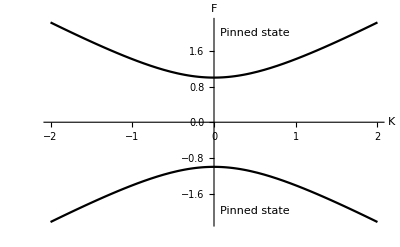

```mathematica
p1=Plot[{√(k^2+Δ^2),-√(k^2+Δ^2)}/.Δ->1,{k,-2,2},AxesLabel->{Style["K",15,Italic],Style["F",15,Italic]},PlotStyle->Black,
Epilog->{
Text["Pinned state",{0.5,2}],
Text["Pinned state",{0.5,-2}]
}
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["bif-diagram-F-k.png",p1];
```